# Slew Effect

```mathematica
c = 299.792458;
mp=938.27203;
md=1875.63;
mHe4=3728.4;
mC12=11178;
mO14 = 13048.92;
```

```mathematica
T2γ[T_(*MeV/u*),m_(*MeV/c^2*),A_]:=(T A+m)/m 
γ2T[γ_,m_,A_]:=(γ-1) m/A(* MeV/u*)
γ2β[γ_]:=√(1-1/γ^2)
β2γ[β_]:=1/(√(1-β^2))
β2ToF[β_,l_]:=l/(β c)(*ns, mm*)
T2Bρ[T_(* MeV *),m_(*MeV/c^2*),A_,Z_]:=(√(2m  (A T)+(A T)^2))/(c Z)(* T-m *)
ToF2β[ToF_ (*ns *),l_(* mm*)]:=l/(ToF c)
T2Bρ[m_,Z_,A_,T_]:= m T2γ[T,m,A] T2β[T,m,A] 1/(Z c)
Bρ2T[m_,Z_,A_,Bρ_]:=1/A( √((Bρ Z c)^2+m^2)-m)
```

```mathematica
T2β[T_,m_,A_]:=γ2β[T2γ[T,m,A]]
T2ToF[T_,m_,A_,l_]:=β2ToF[γ2β[T2γ[T,m,A]],l]
ToF2T[ToF_,l_,m_,A_]:=γ2T[β2γ[ToF2β[ToF,l]],m,A]
```

```mathematica
fp[θ_]:=z0/Cos[θ-60 °]
xpos[θ_]:=z0 Tan[θ-60°]
KE[θ_]:=T/((2mp+T)/(2mp)Tan[θ]^2+1)
```

```mathematica
ToF[T_,z0_,θ_]:=(z0 /Sin[30°+θ °])/(4 c √((T(2mp+T) Cos[θ °]^2)/(4mp+3T+T Cos[2θ °])^2))
```

```mathematica
Manipulate[Plot[ToF[T,z0,θ],{θ,15,70}], {z0,1022.37},{T,258}]
```

```mathematica
xF=-1300;
xB=200;
```

```mathematica
QF[Q_,x_,a_]:=Q Exp[-(x-xF)/a]
QB[Q_,x_,a_]:=Q Exp[-(xB-x)/a]
tF[θ_,β_,τ_,Γ_,T_,z0_]:=ToF[T,z0,θ]+ (xpos[θ]-xF)/(β c)+τ+Γ
tB[θ_,β_,τ_,Γ_,T_,z0_]:=ToF[T,z0,θ]+ (xB-xpos[θ])/(β c)+τ+Γ
```

## Monte Carlo

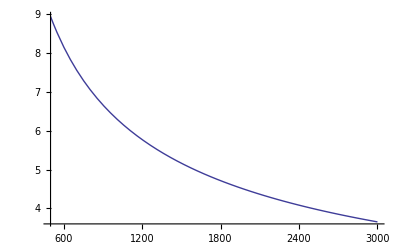

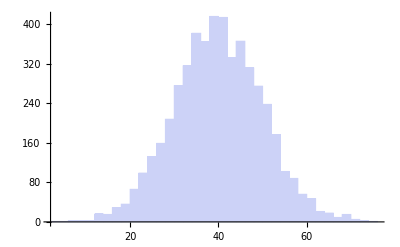

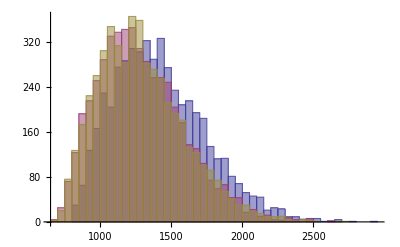

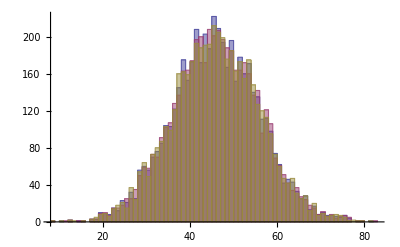

```mathematica
n=5000;
L=100;
β=0.66;
a=500;
Slew=200;
SlewP = 0.5;
walk[Q_]:=Slew/Power[Q,0.5];
Plot[walk[q],{q,500,3000}]
TList =RandomVariate[NormalDistribution[40,10],n];
XList =Table[RandomReal[{0,L}],{i,1,n}];
(*QList=Table[RandomReal[{500,2000}],{i,1,n}];*)
QList=RandomVariate[RayleighDistribution[5],n]*100+800;
(*QList=RandomVariate[PoissonDistribution[100],n]+0.1;*)
q1List=Table[QList[[i]]Exp[(-XList[[i]])/a],{i,1,n}];
w1List=Table[walk[q1List[[i]]],{i,1,n}];
t1List = Table[TList[[i]]+XList[[i]]/(β c)+walk[q1List[[i]]],{i,1,n}];
qt1List=Table[{t1List[[i]],q1List[[i]]},{i,1,n}];
q2List=Table[QList[[i]]Exp[-((L-XList[[i]])/a)],{i,1,n}];
w2List=Table[walk[q2List[[i]]],{i,1,n}];
t2List = Table[TList[[i]]+(L-XList[[i]])/(β c)+walk[q2List[[i]]],{i,1,n}];
qt2List=Table[{t2List[[i]],q2List[[i]]},{i,1,n}];
TavgList=Table[(t1List[[i]]+t2List[[i]])/2,{i,1,n}];
q1TavgList=Table[{TavgList[[i]],q1List[[i]]},{i,1,n}];
Histogram[TList]
Histogram[{QList,q1List,q2List}]
Histogram[{TavgList,t1List,t2List}]
```

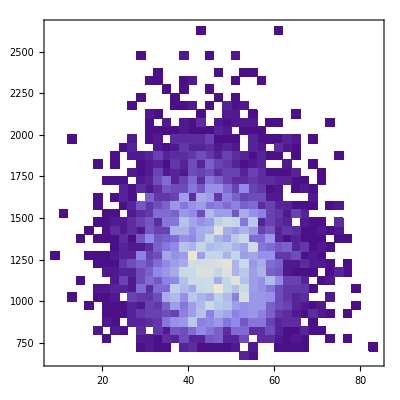

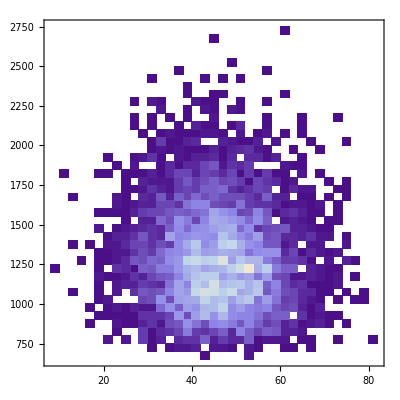

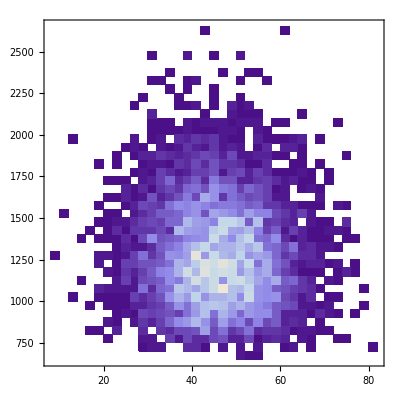

```mathematica
DensityHistogram[qt1List]
DensityHistogram[qt2List]
DensityHistogram[q1TavgList]
```

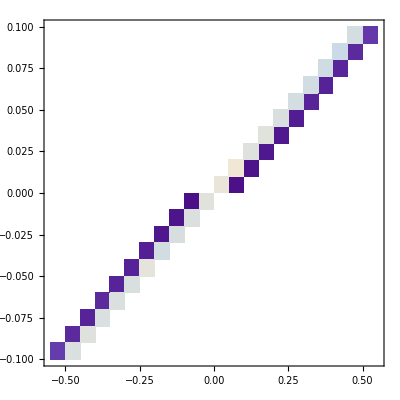

```mathematica
DensityHistogram[Table[{t1List[[i]]-t2List[[i]],Log[q2List[[i]]/q1List[[i]]]},{i,1,n}]]
```

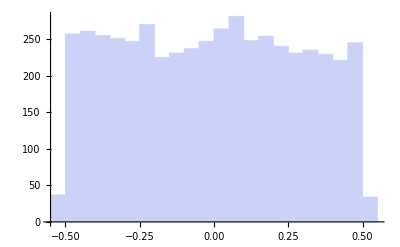

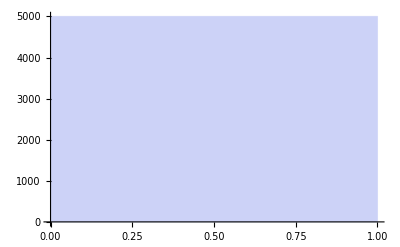

```mathematica
Histogram[Table[t1List[[i]]-t2List[[i]],{i,1,n}]]
Histogram[Table[w1List[[i]]-w2List[[i]],{i,1,n}]]
```

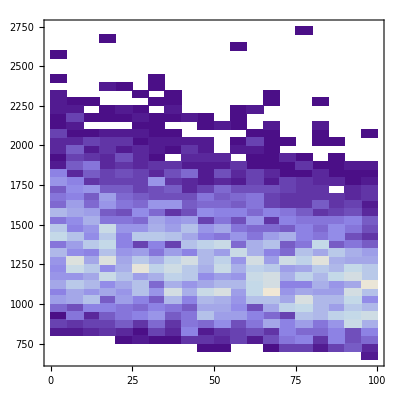

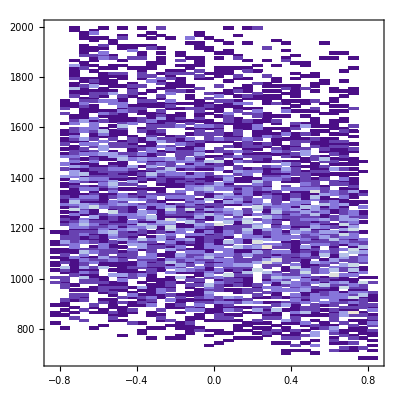

```mathematica
DensityHistogram[Table[{XList[[i]],q1List[[i]]},{i,1,n}]]
DensityHistogram[Table[{t1List[[i]]-t2List[[i]],q1List[[i]]},{i,1,n}],{{-10,10,0.05},{0,2000,10}}]
```

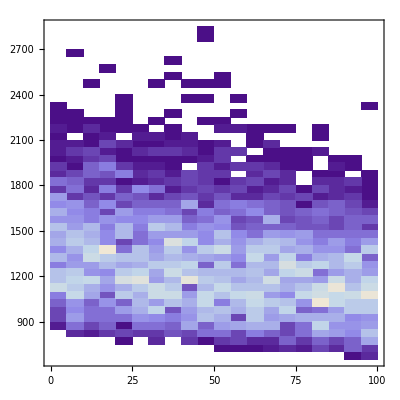

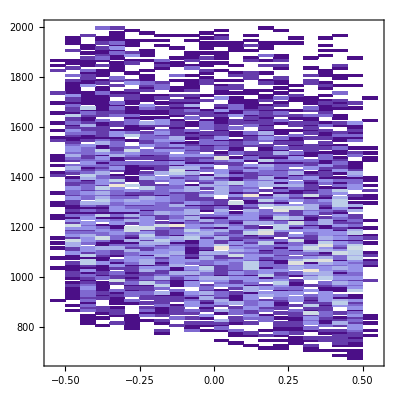

```mathematica
DensityHistogram[Table[{XList[[i]],q1List[[i]]},{i,1,n}]]
DensityHistogram[Table[{t1List[[i]]-t2List[[i]],q1List[[i]]},{i,1,n}],{{-10,10,0.05},{0,2000,10}}]
```

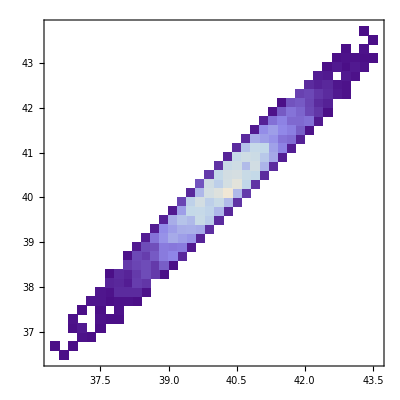

```mathematica
DensityHistogram[Table[{t1List[[i]],t2List[[i]]},{i,1,n}]]
```

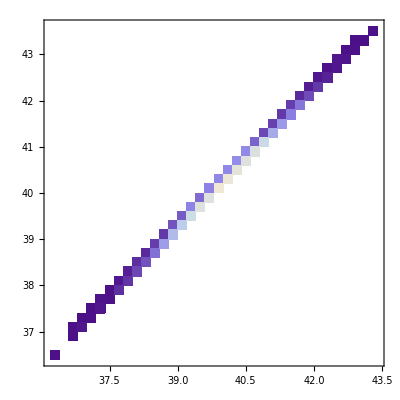

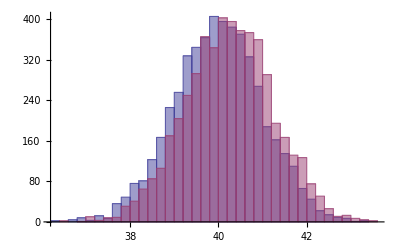

```mathematica
DensityHistogram[Table[{TList[[i]],TavgList[[i]]},{i,1,n}]]
Histogram[{TList,TavgList}]
```

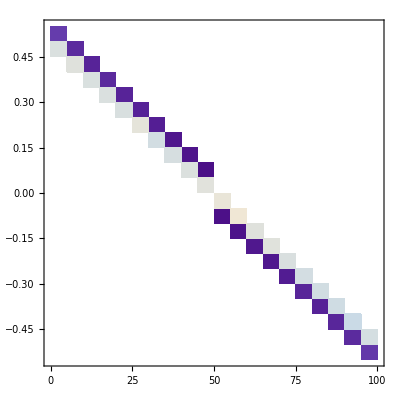

```mathematica
DensityHistogram[Table[{XList[[i]],t2List[[i]]-t1List[[i]]},{i,1,n}]]
```

```mathematica
DensityHistogram[Table[{t2List[[i]]-t1List[[i]]},{i,1,n}]]
```